Current task
-confirm stations can be used for WSE information

Goals:
+Plot showing bathymetry and WSE at various points along river channel, similar to HEC-RAS’s profile plots (done)
+Table of plots for WSE timeseries at each hec-ras cross-section (many) (partially done)


Program outline
1. define order of stations  
2. read station ground elevations from precalculated file (y1)
3. read station locations from fort.14
3. calculate distance down/upstream (x)
4. plot river WSE profile (y1 (x))
5. read fort.61 WSE data from stations of interest (y2(x,t))
6. generate animation of y2(x,t), perhaps using manipulate to scroll. 
7. calculate maxele at each point (y3(x)), plot vs location
8. compare to HEC-RAS solution

# Read Station Locations

```mathematica
(*Read 15 for station locations*)

r="C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\";
fpath15=StringJoin[r,"hurricane.15"];

s15=OpenRead[fpath15];
raw=ReadList[s15,String];

Close[s15];

(*
"Use this scroll bar to find the line # of first + last stations ('start' & 'end')"
Manipulate[raw[[i]],{i,1,Length[raw],1}]

*)
```

# Set Initialization Values

```mathematica
(*start & end of the station list. Assumes the station locations are the same for 61 and 62*)
start=908; (*start line of the stations*)
end=3585; (*end line of the stations*)
(*
(*downstream boundary condition*)
xsecstart=192; (*of the stations, the number of the first of the boundary of interest.*)
xsecend=596; (*of the stations, the number of the end of the boundary of interest. *)
*)


(*02084000*)
(*
xsecstart=51;
xsecend=99;
*)

(*one station at each x-section*)
(*
The challenge here is that each x-section is represented as a different number of stations in ADCIRC (that's a result of the script used to generate the stations, it's not a property of ADCIRC). 
The following list is the length of each x-section. *)
xseclengths={21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 33, 33, 33, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21, 21};
(*what we're interested in, at each timestep, is the average WSE timeseries along each of these strings of stations, excluding any gaps. *) 

(*Once mathematica reads all ~3,000 stations, stationrange tells it where the stations of interest are.*)



bathypath="C:\\Users\\Sam\\Desktop\\Thesis Work\\ADCIRC\\Data reading - bathymetries\\stationBathy.txt";(*text file. one column. one value for each station*)
path61=StringJoin[r,"hurricane.61"]; (*61 to use*)
wseoutpath=StringJoin[r,"river_xsecs_wse_full_hurricane.txt"];(*output path for each boundary node's water surface elevations.*)
avgWSEoutpath=StringJoin[r,"river_xsecs_wse_median_hurricane"];(*output path for average downstream WSE*)
path62=StringJoin[r,"spinup.62"];
davoutpath=StringJoin[r,"DS_boundary_dav_ts.txt"];
```

```mathematica
check=Sum[xseclengths[[i]],{i,1,Length[xseclengths]}]+597
```

2670

# Import Station Locations and Average WSEs

```mathematica
xsecstarts
```

{597,618,639,660,681,702,723,744,765,786,807,828,849,870,891,912,933,954,975,996,1017,1038,1059,1080,1101,1122,1143,1164,1185,1206,1227,1248,1269,1290,1311,1332,1353,1374,1395,1416,1437,1458,1479,1500,1521,1542,1563,1584,1605,1626,1647,1668,1689,1710,1731,1752,1773,1794,1815,1836,1857,1878,1899,1920,1941,1962,1983,2004,2025,2046,2079,2112,2145,2166,2187,2208,2229,2250,2271,2292,2313,2334,2355,2376,2397,2418,2439,2460,2481,2502,2523,2544,2565,2586,2607,2628,2649}

```mathematica
(*stationsAnd61Import[fpath15_,start_,end_,xsecstart_,xsecend_,bathypath_,path61_,wseoutpath_,avgWSEoutpath_,headerinfo_]:={headerinfo,lastx,lasty,lastz,WSEtimeseries}*)
nsections=Length[xseclengths];
xsecstart0=597;
xsecend0=2678;
xsecends=Table[xsecstart0+Sum[xseclengths[[i]]-1,{i,1,j}],{j,1,nsections}];
xsecstarts=Table[0,{nsections}];
xsecstarts[[1]]=xsecstart0;
Do[
xsecstarts[[i]]=xsecends[[i-1]]+1;
,{i,2,nsections}];

stationXYZlists=Table[{0,0,0},{nsections}];
stationWSElists=Table[0,{nsections}];

Dynamic[i]

Do[

raw=stationsAnd61Import[fpath15,start,end,xsecstarts[[i]],xsecends[[i]],bathypath,path61,wseoutpath,StringJoin[avgWSEoutpath,"_xsection_",ToString[i],".txt"],StringJoin["X, Y, Z, and average WSE for section ",ToString[i]]];

(*these are too slow*)
Clear[raw];

,{i,1,nsections}];




(*stationXYZlists[[i]][[j]]
i from 1-> nsections, i is the x-section number as defined by the length table. 
j is 1,2,or 3. 1 is x values, 2 is y values, 3 is z values.
one useful transformation: Transpose[stationXYZlists[[i]]] is a list of {{x,y,z},...} 3D points corresponding to cross-section 
*)
```

```mathematica
stationXYZlists[[1]]
```

{0,0,0}

# Calculate ground elevation for each

```mathematica
maxWSEs=Table[0,{nsections}];
groundE=Table[0,{nsections}];
zs=OpenRead[bathypath];
allZs=ReadList[zs,Word];
allZs=ToExpression[allZs];
Close[zs];


Do[
s=OpenRead[StringJoin[avgWSEoutpath,"_xsection_",ToString[i],".txt"]];
raw=ReadList[s,Number];
maxWSEs[[i]]=Max[raw];
Close[s];

stationindices=xsecstarts[[i]];;xsecends[[i]];
localzs=allZs[[stationindices]];
groundE[[i]]=Max[localzs];

,{i,1,nsections}];

x=Table[i,{i,1,nsections}];
wse=Transpose[Table[{x,maxWSEs}]];
ground=Transpose[Table[{x,-1*groundE}]];
```

ReadList::readn: Invalid real number found when reading from "C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\river_xsecs_wse_median_hurricane_xsection_74.txt".

ReadList::readn: Invalid real number found when reading from "C:\\Users\\Sam\\Desktop\\Thesis Work\\Irene\\run 8 - correct wtiminc daisy chained\\river_xsecs_wse_median_hurricane_xsection_76.txt".

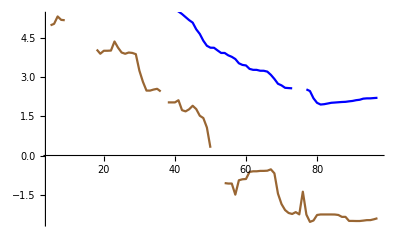

```mathematica
Show[ListPlot[ground,Joined->True,PlotStyle->Brown,PlotRange->Full],ListPlot[wse,Joined->True,PlotStyle->Blue]]

Manipulate[
s=OpenRead[StringJoin[avgWSEoutpath,"_xsection_",ToString[i],".txt"]];
raw=ReadList[s,Number];
Close[s];

real=Re[Fourier[raw]];
imaginary=Im[Fourier[raw]];
{
ListPlot[raw,Joined->True],
ListPlot[Transpose[{real,imaginary}],PlotRange->{{-0.04,-0.01},{-0.2,0.2}}],
Show[ListPlot[real],ListPlot[imaginary,PlotStyle->Red]]
}

,{i,1,nsections,1}]
```

```mathematica
test=Interpolation[raw,Method->"Hermite"];
testft=FourierTransform[test[j],j,w];
testft
```

FourierTransform[InterpolatingFunction[{{1., 2880.}}, <>][j],j,w]

```mathematica
i=1;
s=OpenRead[StringJoin[avgWSEoutpath,"_xsection_",ToString[i],".txt"]];
raw=ReadList[s,Number];
Mean[raw]
```

7.92009